Результаты по методу Рунге-Куты

|   x |   y
 |  0.78540 |  0.50000
 |  0.83540 |  0.49750
 |  0.88540 |  0.49003
 |  0.93540 |  0.47767
 |  0.98540 |  0.46053
 |  1.03540 |  0.43879
 |  1.08540 |  0.41267
 |  1.13540 |  0.38242
 |  1.18540 |  0.34835
 |  1.23540 |  0.31080

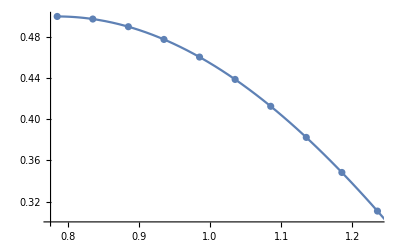

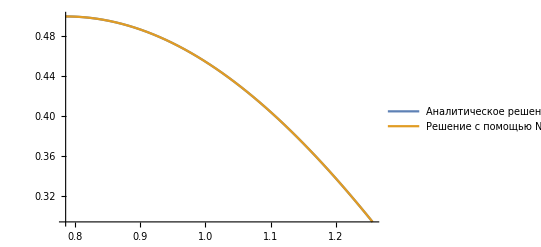

```mathematica
(*Вариант 4*)
f[x_,y_]:=(Cos[x])^2-y*Tan[x];
h=0.05;
a=0.25*π;b=0.4*π;
m=Floor[(b-a)/h]+1;
y0=0.5;
x0=a;
(*Расчёт по методу Рунге-Куты 4-го порядка*)
rk4[f_,x0_,y0_,h_,m_]:=Block[
{k1,k2,k3,k4,x=x0,y=y0,t,k},
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
t=Table[
{x,y}={x+h,y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6},
{k,m-1}
];
t=Prepend[t,{x0,y0}];
Return[t]
]
tab1:=rk4[f,x0,y0,h,m];
gr1:=ListPlot[tab1]
Print["Результаты по методу Рунге-Куты"]
lst={{},{"  x","  y"}};
PaddedForm[TableForm[tab1,TableHeadings->lst],{5,5}]
g[x_]:=0.5*Sin[2*x]
gr2:=Plot[g[x],{x,a,b}]
Show[{gr1,gr2}]
(*Для сравнения воспользуемся встроенной функцией NDSolve*)
Clear[v,u];
solution=NDSolve[{v'[u]==f[u,v[u]],v[x0]==y0},v,{u,a,b}];
g4[u_]:=v[u]/.solution;
gr5:=Plot[{g[x],g4[x]},{x,a,b}, PlotLegends->{"Аналитическое решение","Решение с помощью NDSolve"}]
Show[{gr5}]
```